```mathematica
Clear[DeleteEdgeQuest]
```

```mathematica
DeleteEdgeQuest[g_]:=Block[{ symbols=SymbolRange[g]},
{
Monitor[
Table[
With[
{cond=ToLogical[EdgeDelete[g,e]]&&Symbol["x"<>ToString[e[[1]]]]==Symbol["x"<>ToString[e[[2]]]]},
{ChromaticPolynomial[EdgeContract[g,e],4]==Length[Solve[cond,symbols]]}
]
,{e,EdgeList[g]}],
e]
}
]
```

```mathematica
EdgeList[ReadGrof[50000]]
```

{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,2<->9,2<->10,3<->5,3<->7,3<->8,3<->9,3<->11,3<->12,3<->13,4<->5,4<->6,4<->8,5<->6,5<->7,5<->8,5<->10,5<->11,5<->12,6<->8,6<->9,6<->10,7<->12,8<->9,8<->13,9<->13,11<->12}

```mathematica
Monitor[Table[{k,Chrom[k]/24,DeleteEdgeQuest[ReadGrof[k]]},{k,50000,50000}],k]
```

{{50000,4,{{{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True}}}}}

```mathematica
Clear[DeleteEdgeQuest]
```

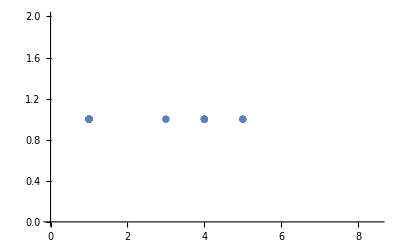

```mathematica
ListPlot[Map[{#[[2]],#[[3]]}&,%]]
```